```mathematica
λs = {0.2, 0.5, 1.0, 1.5, 2.5};
```

```mathematica
σnh=Table[ToExpression[Import["~/Projects/nh_quasiperiodic_disorder/Fig2/lambda="<>ToString[NumberForm[i,{2,1}]]<>".csv"]][[2;;-1]],{i,λs}];
```

```mathematica
σh = Table[ToExpression[Import["~/Projects/nh_quasiperiodic_disorder/FigS2/datas/lambda="<>ToString[NumberForm[i,{2,1}]]<>".csv"]][[2;;-1]],{i,{2.0, 0.5}}];
```

```mathematica
σ = σnh ~ Join~ σh;
```

```mathematica
λs = {0.2, 0.5, 1.0, 1.5, 2.5,2.0, 0.5};
```

```mathematica
lm = Table[LinearModelFit[σ[[i]][[200;;-1]],x,x],{i, Length@σ}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
lm[[3]] = LinearModelFit[σ[[3]][[1000;;-1]],x,x]
```

FittedModel[…]

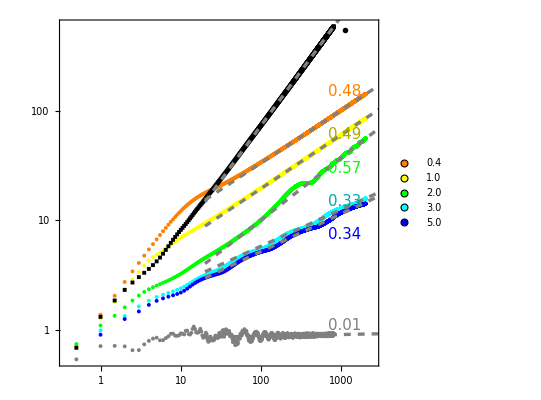

```mathematica
fig2a = Show[ListPlot[σ[[6;;7]], PlotStyle->{{Gray},{ Black}},PlotTheme->"Frame",PlotMarkers->{Automatic,Tiny},FrameTicks->{{{{Log[0.1],"0.1"},{Log[1],"1"},{Log[10],"10"},{Log[100],"100"}},None},{{{Log[0.1], "0.1"},{Log[1],"1"},{Log[10],"10"},{Log[100],"100"},{Log[1000],"1000"}},None}},PlotRange->{{-1, 7.8},All},LabelStyle->{FontFamily->"Times", FontColor-> Black, 23},ImageSize->{295}, Epilog->{Inset[Style[ToString[Round[lm[[1]]["BestFitParameters"][[2]],0.01]], FontFamily->"Times", Orange, 15 ], {7, 5}],Inset[Style[ToString[Round[lm[[2]]["BestFitParameters"][[2]],0.01]], FontFamily->"Times", Darker[Yellow], 15 ], {7, 4.1}],Inset[Style[ToString[Round[lm[[3]]["BestFitParameters"][[2]],0.01]], FontFamily->"Times", Green, 15 ], {7, 3.4}],Inset[Style[ToString[Round[lm[[4]]["BestFitParameters"][[2]],0.01]], FontFamily->"Times", Darker[Cyan], 15 ], {7, 2.7}],Inset[Style[ToString[Round[lm[[5]]["BestFitParameters"][[2]],0.01]], FontFamily->"Times", Blue, 15 ], {7, 2}],Inset[Style[ToString[Round[lm[[6]]["BestFitParameters"][[2]],0.01]], FontFamily->"Times", Gray, 15 ], {7, 0.1}],Inset[Style[ToString[Round[lm[[7]]["BestFitParameters"][[2]],0.01]], FontFamily->"Times", Black, 15 ], {7, 6.3}]}],ListPlot[σ[[1;;5]], PlotStyle->{{Orange}, {Yellow}, {Green}, {Cyan},{Blue}},PlotMarkers->{Graphics[Disk[]], Tiny}, PlotLegends->Placed[PointLegend[Table[Style[ToString[NumberForm[2*λs[[i]],{2,1}]], FontSize->15],{i, {1,2,3,4,5}}],LegendFunction->(Framed[#,RoundingRadius->10,Background->Opacity[0.8,White],FrameStyle->Gray]&),LegendLayout->Automatic, LabelStyle->{FontFamily->"Times", FontColor-> Black, 5},LegendMargins->{{0, 0}, {0, 0}}], {0.24, 0.61}](*,FrameTicks->{{{{Log[0.1],"0.1"},{Log[1],"1"},{Log[10],"10"},{Log[100],"100"}},None},{{{Log[0.1], "0.1"},{Log[1],"1"},{Log[10],"10"},{Log[100],"100"},{Log[1000],"1000"}},None}},PlotRange->All,LabelStyle->{FontFamily->"Times", FontColor-> Black, 23},ImageSize->{295}, Epilog->{Inset[Style[ToString[Round[lm[[1]]["BestFitParameters"][[2]],0.01]], FontFamily->"Times", Orange, 15 ], {7, 5}],Inset[Style[ToString[Round[lm[[2]]["BestFitParameters"][[2]],0.01]], FontFamily->"Times", Darker[Yellow], 15 ], {7, 4.1}],Inset[Style[ToString[Round[lm[[3]]["BestFitParameters"][[2]],0.01]], FontFamily->"Times", Green, 15 ], {7, 3.4}],Inset[Style[ToString[Round[lm[[4]]["BestFitParameters"][[2]],0.01]], FontFamily->"Times", Darker[Cyan], 15 ], {7, 2.7}],Inset[Style[ToString[Round[lm[[5]]["BestFitParameters"][[2]],0.01]], FontFamily->"Times", Blue, 15 ], {7, 2}],Inset[Style[ToString[Round[lm[[6]]["BestFitParameters"][[2]],0.01]], FontFamily->"Times", Purple, 15 ], {7, 0.1}],Inset[Style[ToString[Round[lm[[7]]["BestFitParameters"][[2]],0.01]], FontFamily->"Times", Red, 15 ], {7, 6.3}]}*)],Plot[Table[lm[[i]][x],{i, Length@λs}],{x,Log[20],10}, PlotStyle->{Gray, Dashed, Thickness[0.006]}], AspectRatio->1]
```

```mathematica
datas=Table[ToExpression[Import["~/Projects/nh_quasiperiodic_disorder/Fig2/datas/re"<>ToString[NumberForm[i,{2,1}]]<>"_im"<>ToString[NumberForm[j,{2,1}]]<>".csv"]][[2;;-1]],{i,Range[0,2.5,0.1]}, {j,Range[0,2.5,0.1] }];
```

```mathematica
δs = ParallelMap[LinearModelFit[#[[30;;500]],x,x]["BestFitParameters"][[2]]&, datas, {2}];
```

```mathematica
δs[[1;;11, 1;;11]]=ParallelMap[LinearModelFit[#[[40;;320]],x,x]["BestFitParameters"][[2]]&, datas[[1;;11, 1;;11]], {2}];
```

```mathematica
δs[[12;;-1, 1]] = ParallelMap[LinearModelFit[#[[5;;120]],x,x]["BestFitParameters"][[2]]&, datas[[12;;-1, 1]]];
δs[[9,7]] = LinearModelFit[datas[[9,7]][[20;;-1]],x,x]["BestFitParameters"][[2]];
```

```mathematica
es = Transpose@Flatten[Table[{i, j},{i,Range[0,2.5,0.1]}, {j,Range[0,2.5,0.1] }],1];
```

```mathematica
plotδs=Transpose@Join[es, {Flatten@δs}];
```

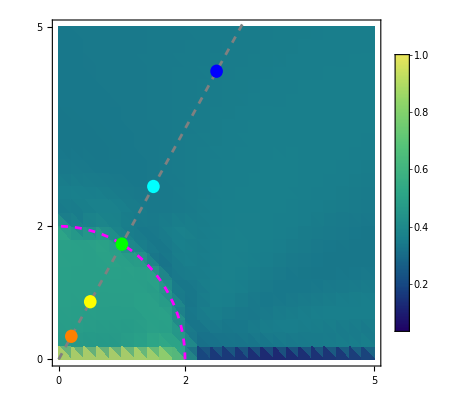

```mathematica
fig2b =Show[ListDensityPlot[plotδs, (*ColorFunction->(RGBColor[#,#,#]&),*)ColorFunction->(ColorData["BlueGreenYellow"][#]&),(*InterpolationOrder->0,*)PlotRange->All, FrameTicks->{{{0,{1, "2"},{2.5, "5"}},None},{{0,{1, "2"},{2.5, "5"}},None}},PlotLegends->Placed[BarLegend[Automatic, LegendMarkerSize->{15, 200},(*Ticks->{0.0,1},*)LabelStyle->{FontFamily->"Times New Roman",18,Black}], Right], PlotRangePadding->None,LabelStyle->{FontFamily->"Times", FontColor-> Black, 23}, ImageSize->{300}],Plot[Tan[π/3]x, {x, 0, 1.5}, PlotStyle->{Gray, Dashed}],ParametricPlot[{Cos[t],Sin[t]},{t,0,Pi/2}, PlotStyle->{RGBColor[1,0,1], Dashed}],Graphics[{Orange, Disk[{λs[[1]] Cos[π/3], λs[[1]] Sin[π/3]},.05],Yellow,  Disk[{λs[[2]] Cos[π/3], λs[[2]] Sin[π/3]},.05], Green, Disk[{λs[[3]] Cos[π/3], λs[[3]] Sin[π/3]},.05], Cyan, Disk[{λs[[4]] Cos[π/3], λs[[4]] Sin[π/3]},.05], Blue,Disk[{λs[[5]] Cos[π/3], λs[[5]] Sin[π/3]},.05]}]]
```

```mathematica
Fig2 = ListPlot[{{0,0}},PlotStyle->Opacity[0],PlotRange->{{0,1},{0,1}},ImageSize->{660,Automatic},Axes->None,Epilog->{Inset[fig2a,{.225,0.5}], Inset[fig2b,{.745,0.51}],Inset[Rotate[Row[{Style["Im ",23,FontFamily->"Times"],Style["V",23,FontFamily->"Times",Italic]}],Pi/2],{0.48,0.57}],Inset[Rotate[Row[{Style["X(t)",23,FontFamily->"Times",Italic]}],Pi/2],{0.02,0.58}], Inset[Row[{Style["Re ",23,FontFamily->"Times"],Style["V",23,FontFamily->"Times",Italic]}], {0.715, 0.04}],Inset[Row[{Style["t",23,FontFamily->"Times", Italic]}], {0.25, 0.04}], Inset[Row[{Style["δ",23,FontFamily->"Times"]}], {0.94, 0.84}],Inset[Style["(a)",26,FontFamily->Times],{.09,0.9}],Inset[Style["(b)",26,FontFamily->Times],{.54,0.9}]}, AspectRatio->0.47]
```

-Graphics-

```mathematica
Export["/Users/xingzy/Projects/nh_quasiperiodic_disorder/Fig2/Fig2.pdf",Fig2,"PDF"]
```

/Users/xingzy/Projects/nh_quasiperiodic_disorder/Fig2/Fig2.pdf